## Numerical Analysis — Problem Set 3 — Starting Applications Programs

## Due Tuesday, Sep. 20 (beginning of class)

## We are leaving the HP-25 Owner’s Handbook behind and launching into Chapter 1 of the HP-25 Applications Programs book. These problems relate to the Plotting/Graphing program and the Base Conversion programs.

### 1. Plotting/Graphing

After you have keyed in the Plotting/Graphing program on p. 7 of the Applications Programs book, use it to plot three trajectories:

(a) 0.25 time interval in seconds (abbreviated s), 9.8 acceleration of gravity in meters per second per second, (abbreviated m/s^2), 30.ba initial angle, 20 initial speed in meters/second (abbreviated m/s)
(b) 0.25 s, 9.8 m/s^2, 45.ba, 20 m/s
(c) 0.25 s, 9.8 m/s^2, 60.ba, 20 m/s

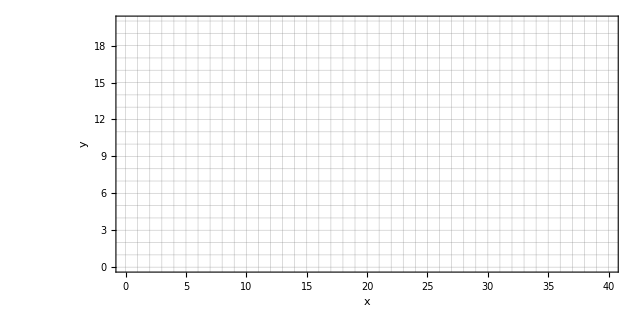

```mathematica
Plot[{},{x, 0, 40}, PlotRange->{{0,40},{0,20}},GridLines->{Range[0, 40, 1],Range[0,20, 1]}, AxesLabel->{x, y}, Ticks->{Range[0,40, 5], Range[0,20, 5]}, AspectRatio->1/2, Frame->True]
```

### 2. Including Air Resistance

Examine the program and find the lines where this equation was incorporated:

x=v_x t

Change the lines to this new formula for x:

x=(v_x v_terminal)/g(1-e^(-gt/v_terminal))

v_terminal is a new parameter that accounts for air resistance (it is known as the terminal velocity). You are going to need to store that new parameter in another register. Since R_0 to R_4 are already assigned, R_5 would be a good choice. Document your program in the usual format (a program form is attached).

### 3. Plot with Air Resistance

Re-do your plot of trajectory (a) with your new program and v_terminal=30 m/s.  (All other parameters should be the same as trajectory (a) above.)

```mathematica
Plot[{},{x, 0, 40}, PlotRange->{{0,40},{0,20}},GridLines->{Range[0, 40, 1],Range[0,20, 1]}, AxesLabel->{x, y}, Ticks->{Range[0,40, 5], Range[0,20, 5]}, AspectRatio->1/2, Frame->True]
```

-Graphics-

To be fair, I have to admit that the formula for y which was y=v_y t-1/2 g t^2 really should to be modified to include air resistance too. But if you fire at low angles, that modification doesn’t matter much.

### 4. Converting from Base 2 to Base 10

Convert 1000000000 in base 2 (there are 9 zeros in that number) to a number in base 10.

### 5. Converting from Base 10 to Base 16 and Base 2

(a) Convert 48879 in base 10 to base 16.

(b) In base 16, we could really use more numerals to choose from, because each digit goes from 00 to 15. Here is how the digits are usually represented in base 16:

Instead of 00 just write 0.
Instead of 01 just write 1.
Instead of 02 just write 2.
...
Instead of 07 just write 7.
Instead of 08 just write 8.
Instead of 09 just write 9.
Instead of 10 just write A.
Instead of 11 just write B.
Instead of 12 just write C.
Instead of 13 just write D.
Instead of 14 just write E.
Instead of 15 just write F.

Convert whatever you got in Part (a) using these conventions.

(c) It is common to prefix base sixteen numbers with 0x to emphasize that they are base 16. Here is how the khaki color on the Deep Springs website is stuffed into three bytes on a video card: 0xFBFCE0. 0xFB represents the red value. 0xFC represents the green value, and 0xE0 represents the blue value.

What are the red, green, and blue values in base 10?

NB: You don’t need any program to do parts (b) and (c). For example, for the red in part (c), you just need to know that F is in the 16’s place and F represents 15, so to 15x16 you need to add what B represents, which is 11.

(d) Convert 0.2 in base 10 to base 2.  This one is amusing: such an easy number in base 10 (and such an easy fraction, it is just 1/5) has no easy representation in base 2!